# Comparing SSA model to experimental results

Code for forecasting extinction risk under different levels of temporal autocorrelation for a specific time series and time scale. This notebook contains all the code used to generate the simulations and create Fig. 5; for easy replication of that figure, download the required MX files from the repository beforehand (files). Subfigures from this notebook were compiled using Adobe Illustrator 2024.

## Background Functions

Run this section once to define the TPC and the necessary functions for the SSA model. Before running, define the directory you want to import to or export from.

```mathematica
directory="/directory/";

(*parameters for K and lactin2 model fit*)
K=5000;
a=0.044;
b=-1.774;
tmax=35.254;
deltat=5.435;

(*lactin2 equation*)
netgrowth[temp_]:=Module[
{a=0.044,
b=-1.774,
tmax=35.254,
deltat=5.435,
est},
est=Exp[a*temp]-Exp[a*tmax-((tmax-temp)/deltat)]+b;
est
];

(*define birth function*)
bTemp[temp_]:=Module[
{a=0.044,
birth},
birth=Exp[a*temp];
birth
];
rmax=FindMaximum[netgrowth[x],x];
topt=x/.rmax[[2]];
rmax=rmax[[1]];
d1=netgrowth[topt]/K;

(*define death function, adjusted so that K declines over time*)
dTemp[temp_,n_,t_]:=Module[
{a=0.044,
b=-1.774,
tmax=35.254,
deltat=5.435,
topt=25.0341,
d1=0.000103037},
Exp[a*tmax-((tmax-temp)/deltat)]-b+(d1+d1*t/56)*n
];

(*calculate persistence boundaries*)
lactin2[T_,{a_,b_,tmax_,δT_}]:=Exp[a T]-Exp[a tmax-((tmax-T)/δT)]+b;
paramsfit={0.044,-1.774,35.254,5.435};
w[T_]:=lactin2[T,paramsfit];
divisions=40;
σTrange=Range[0.01,8.01,8/divisions];
μTrange=Range[10,35,25/divisions];

Clear[T];
moments=Flatten[ParallelTable[Module[{mean,var,skew,kurt},
mean=NExpectation[w[T],T\[Distributed]NormalDistribution[μT,σT]];
var=NExpectation[(w[T]-mean)^2,T\[Distributed]NormalDistribution[μT,σT]];
skew=NExpectation[((w[T]-mean))^3,T\[Distributed]NormalDistribution[μT,σT]]/var^(3/2);
kurt=NExpectation[(w[T]-mean)^4,T\[Distributed]NormalDistribution[μT,σT]]/(var^2)-3;
{μT,σT,mean,var,skew,kurt,If[mean>0,Log10[var/mean],10]}],{σT,σTrange},{μT,μTrange}],1];
```

## SSA Model

Run simulations and store extinction outcomes. Choose which temperature time series to use by changing the value of ‘series’ (temps = white noise, temps2 = pink noise, temps3 = brown noise). The SSA occurs in the ParallelDo loop over the parameters specified in ‘μTrange’ and ‘σTrange.’ This code is quite slow; if you have already downloaded the MX files, skip to the next block of code.

```mathematica
(*experimental temperature time series*)
tempsequence={28.105,20.9738,21.7771,31.756,28.6008,28.3445,28.4703,23.9669,30.6391,24.6075,27.7707,30.1283,24.8433,24.1295,23.2893,27.3607,32.3506,20.818,25.63,25.3925,29.9094,23.1105,25.0783,26.2814,25.2352,24.9217,25.5506,26.0331,26.4504,16.71,23.5496,22.7367,21.6555,24.0484,26.198,29.3465,33.29,30.9471,25.,24.21,24.5286,26.7995,23.6345,20.6535,28.2229,28.878,18.6904,19.6306,25.1567,27.46,21.2635,25.3137,22.8324,25.9516,26.623,19.0529,22.3352,26.3655,25.4714,26.1152,23.802,27.2633,23.2005,27.5613,25.7098,34.1517,17.6494,22.0094,20.2919,22.4387,26.7107,31.3096,21.3992,23.4638,22.2293,21.5297,24.7648,26.5362,24.2902,29.5213,28.7365,18.244,24.6863,19.3609,29.0262,23.0192,21.895,27.6648,25.79,30.3694,21.122,27.1676,22.9265,24.4494,20.4787,26.8895,22.1208,25.8705,26.9808,27.8792,27.0735,23.7186,27.9906,29.182,22.6393,23.377,24.37,23.8848,19.8717,29.7081,20.0906,22.54};
tempsequence2={19.6306,20.818,21.122,23.7186,28.3445,29.3465,27.6648,27.0735,24.7648,30.3694,27.5613,27.46,26.1152,27.1676,24.0484,25.4714,25.8705,23.0192,26.4504,29.7081,25.63,32.3506,26.9808,25.3137,28.878,22.7367,29.182,29.9094,26.7995,25.3925,22.4387,23.4638,24.2902,25.1567,24.9217,22.9265,26.623,27.8792,23.2893,22.6393,20.4787,23.9669,25.5506,24.5286,19.8717,26.8895,26.2814,29.5213,31.756,31.3096,26.5362,34.1517,30.1283,28.6008,33.29,29.0262,28.7365,28.2229,28.4703,24.21,24.4494,30.9471,25.,27.2633,25.9516,23.377,21.895,24.6863,24.8433,24.6075,20.0906,21.5297,25.79,23.1105,21.3992,17.6494,22.54,22.3352,25.2352,21.2635,26.3655,18.6904,20.2919,24.37,23.6345,25.0783,23.5496,22.2293,21.7771,22.0094,22.1208,19.0529,16.71,18.244,21.6555,23.2005,24.1295,27.3607,23.802,19.3609,20.6535,25.7098,26.7107,26.198,28.105,30.6391,23.8848,26.0331,27.9906,27.7707,20.9738,22.8324};
tempsequence3={22.9265,22.8324,23.377,23.6345,23.802,23.8848,25.1567,24.6863,23.2893,22.4387,21.895,20.4787,20.9738,21.6555,20.0906,21.3992,20.6535,22.2293,23.2005,23.5496,25.2352,26.3655,25.63,25.7098,24.6075,24.2902,22.54,24.0484,24.4494,23.4638,24.9217,25.,23.7186,23.1105,22.7367,22.1208,22.3352,21.5297,21.2635,19.3609,19.6306,18.6904,18.244,16.71,17.6494,19.0529,20.2919,20.818,21.7771,21.122,19.8717,22.0094,23.0192,24.1295,25.3137,26.2814,25.9516,26.0331,27.5613,26.8895,26.4504,25.79,26.198,25.3925,26.7107,30.1283,29.9094,28.878,27.7707,28.3445,28.105,27.9906,26.5362,29.0262,29.182,30.6391,30.9471,31.3096,30.3694,32.3506,33.29,34.1517,31.756,29.7081,27.6648,28.7365,27.1676,28.2229,29.5213,26.9808,26.1152,27.2633,26.623,27.46,27.3607,27.8792,28.4703,29.3465,27.0735,25.8705,25.5506,28.6008,26.7995,25.4714,24.8433,24.7648,25.0783,23.9669,24.37,24.21,24.5286,22.6393};

(*add zero to end of each series to keep algorithm from crashing at final step*)
temps=Join[(tempsequence-25)/3.5,{0}]; (*white*)
temps2=Join[(tempsequence2-25)/3.5,{0}]; (*pink*)
temps3=Join[(tempsequence3-25)/3.5,{0}]; (*brown*)

series=temps; (*pick series here*)

(*delineate parameter range*)
divisions=40;
σTrange=Range[0.01,8.01,8/divisions]; 
μTrange=Range[10,35,25/divisions];
output={};
reps=40;(*40*)

SetSharedVariable[output];
ParallelDo[
extinct=0;
Do[
n=500;
t=0;
tcount=1;
T=series[[tcount]]*σ+μ;
Tinterval=tnext=0.5;

While[t<56,
evector={bTemp[T]*n,dTemp[T,n,t]*n};
t+=RandomReal[ExponentialDistribution[Total[evector]]];
event=RandomChoice[evector->{1,2}];
If[event==1,n++,n--];
If[n==0,extinct++;Break[]];
If[t>=tnext,tcount++;T=series[[tcount]]*σ+μ;tnext+=Tinterval]],{reps}];
If[n<10&&n!=0,extinct++];
AppendTo[output,{μ,σ,N[1-extinct/reps]}],{μ,μTrange},{σ,σTrange}];

Which[series==temps,color="white",series==temps2,color="pink",series==temps3,color="brown"];
Export[directory<>"SSA2_"<>color<>".m",output,"MX"]
```

Download the needed MX files and generate plots shown in Fig. 5a-c.

```mathematica
SSAwhite=Import[directory<>"SSA2_white.m","MX"];
SSApink=Import[directory<>"SSA2_pink.m","MX"];
SSAbrown=Import[directory<>"SSA2_brown.m","MX"];

wresults={{25.0284,3.29531,0.83333},{27.0072,3.3534,0.5},{28.0454,3.31001,0.41667},{29.0142,3.33436,0.16667},{30.0345,3.25052,0}};
presults={{24.9767,3.30643,0.91667},{26.9774,3.37776,0.75},{28.0292,3.37251,0.41667},{28.9799,3.43065,0.08333},{30.0191,3.39953,0}};
bresults={{25.0567,3.4065,1},{27.0608,3.3472,0.16667},{28.0491,3.39566,0},{29.0499,3.39271,0},{29.9115,3.44396,0}};

newmap[x_]:=Blend[{RGBColor["#ffffd9"],RGBColor["#edf8b1"],RGBColor["#c7e9b4"],RGBColor["#7fcdbb"],RGBColor["#41b6c4"],RGBColor["#4eb3d3"],RGBColor["#2b8cbe"],RGBColor["#0868ac"],RGBColor["#084081"]},1-x];

SSAwhiteplot=Show[ListContourPlot[SSAwhite,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Proportion\n Persisting",LabelStyle->{Darker[Gray],13}],Left],PlotLabel->Style["White Noise (γ = 0)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["a)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,wresults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,wresults}]}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSApinkplot=Show[ListContourPlot[SSApink,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Pink Noise (γ = 1)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["b)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,presults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,presults}]}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAbrownplot=Show[ListContourPlot[SSAbrown,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Brown Noise (γ = 2)",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]],
Epilog->
{{Text[Style["c)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,bresults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,bresults}]}],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAs=GraphicsRow[{SSAwhiteplot,SSApinkplot,SSAbrownplot},Spacings->0,ImageSize->1000]
(*Export[directory<>"SSAs.pdf",SSAs,ImageResolution->1000]*)
```

-Graphics-

Generate additional plots over a longer timescale to see how the envelope of persistence contracts when tmax is greater; use to generate Fig S2.

```mathematica
SSAwhite2=Import[directory<>"SSA2_t1009_20reps_white.m","MX"];
SSApink2=Import[directory<>"SSA2_t1009_20reps_pink.m","MX"];
SSAbrown2=Import[directory<>"SSA2_t1009_20reps_brown.m","MX"];

SSAwhiteplot2=Show[ListContourPlot[SSAwhite2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,PlotLegends->Placed[BarLegend[Automatic,LegendLabel->"Proportion\n Persisting",LabelStyle->{Darker[Gray],13}],Left],PlotLabel->Style["White Noise (γ = 0), t_max = 1009",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]](*,
Epilog->
{{Text[Style["a)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,wresults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,wresults}]}*)],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSApinkplot2=Show[ListContourPlot[SSApink2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Pink Noise (γ = 1), t_max = 1009",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]](*,
Epilog->
{{Text[Style["b)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,presults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,presults}]}*)],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAbrownplot2=Show[ListContourPlot[SSAbrown2,InterpolationOrder->0,Contours->19,ColorFunction->newmap,(*PlotLegends->Placed[Automatic,Left],*)PlotLabel->Style["Brown Noise (γ = 2), t_max = 1009",15],ImageSize->310,Frame->True,FrameStyle->16,FrameLabel->{"Mean Temperature, μ_T","SD of Temperature, σ_T"},GridLines->{μTrange+.5 25/40,σTrange+.5 8/40},GridLinesStyle->Directive[Opacity[0.4],Thickness[0.0001]](*,
Epilog->
{{Text[Style["c)",White,17],{11.2,7.7}]},
Table[{Directive[Black],PointSize[.045],Point[{point[[1]],point[[2]]}]},{point,bresults}],
Table[{Directive[newmap[point[[3]]]],PointSize[.035],Point[{point[[1]],point[[2]]}]},{point,bresults}]}*)],
ListContourPlot[moments[[1;;,{1,2,7}]],InterpolationOrder->3,Contours->{0,Log10[2]},ContourStyle->{{Thickness[0.01],Opacity[1],Gray},{Thickness[0.01],Opacity[1],Black}},ContourShading->None]];

SSAs=GraphicsRow[{SSAwhiteplot2,SSApinkplot2,SSAbrownplot2},Spacings->0,ImageSize->1000]
(*SSAs=GraphicsGrid[{{SSAwhiteplot,SSApinkplot,SSAbrownplot},{SSAwhiteplot2,SSApinkplot2,SSAbrownplot2}},Spacings->0,ImageSize->1000]*)
Export[directory<>"SSAs_t1009.pdf",SSAs,ImageResolution->1000];
```

-Graphics-

## Compare results to the running mean

Use this code to calculate the running mean and generate Fig. 5d-f.

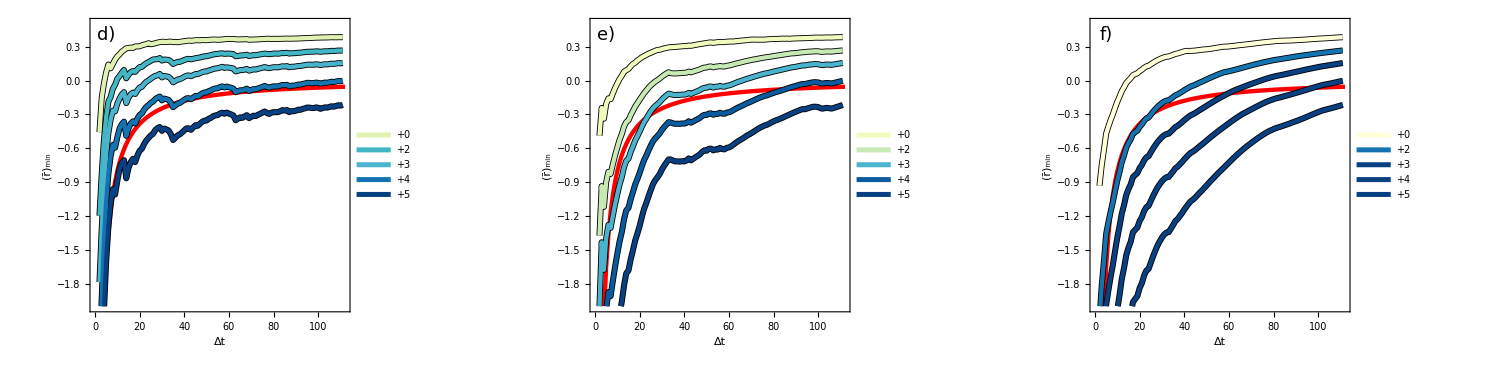

```mathematica
ExtTime[t_,α_,N0_]:=r/.NSolve[1==N0 r/α Exp[r t]/(((r/α)-N0)+N0 Exp[r t]),r,Reals][[1]];

white=Table[{i,Min[MovingAverage[w[tempsequence],i]]},{i,2,Length[tempsequence]-1}];
pink=Table[{i,Min[MovingAverage[w[tempsequence2],i]]},{i,2,Length[tempsequence2]-1}];
brown=Table[{i,Min[MovingAverage[w[tempsequence3],i]]},{i,2,Length[tempsequence3]-1}];

white2=Table[{i,Min[MovingAverage[w[tempsequence+2],i]]},{i,2,Length[tempsequence]-1}];
pink2=Table[{i,Min[MovingAverage[w[tempsequence2+2],i]]},{i,2,Length[tempsequence2]-1}];
brown2=Table[{i,Min[MovingAverage[w[tempsequence3+2],i]]},{i,2,Length[tempsequence3]-1}];

white3=Table[{i,Min[MovingAverage[w[tempsequence+3],i]]},{i,2,Length[tempsequence]-1}];
pink3=Table[{i,Min[MovingAverage[w[tempsequence2+3],i]]},{i,2,Length[tempsequence2]-1}];
brown3=Table[{i,Min[MovingAverage[w[tempsequence3+3],i]]},{i,2,Length[tempsequence3]-1}];

white4=Table[{i,Min[MovingAverage[w[tempsequence+4],i]]},{i,2,Length[tempsequence]-1}];
pink4=Table[{i,Min[MovingAverage[w[tempsequence2+4],i]]},{i,2,Length[tempsequence2]-1}];
brown4=Table[{i,Min[MovingAverage[w[tempsequence3+4],i]]},{i,2,Length[tempsequence3]-1}];

white5=Table[{i,Min[MovingAverage[w[tempsequence+5],i]]},{i,2,Length[tempsequence]-1}];
pink5=Table[{i,Min[MovingAverage[w[tempsequence2+5],i]]},{i,2,Length[tempsequence2]-1}];
brown5=Table[{i,Min[MovingAverage[w[tempsequence3+5],i]]},{i,2,Length[tempsequence3]-1}];

imsize=310;
arat=.7;

wplot=Show[ListLinePlot[ParallelTable[{t,ExtTime[t,α,N0]},{t,2,Length[tempsequence]}],PlotStyle->{Thickness[0.01],Red},PlotRange->{{0,Length[tempsequence]},{-2,.5}},Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","(r̄)_min"},AspectRatio->arat,ImageSize->imsize,
Epilog->{Text[Style["d)",Black,18],{5,.4}]}],
ListLinePlot[{white,white2,white3,white4,white5},PlotStyle->{{Thickness[.014],Black}},PlotRange->{{0,Length[tempsequence]},{-2,.5}}],
ListLinePlot[{white,white2,white3,white4,white5},PlotLegends->Placed[{"+0","+2","+3","+4","+5"},{Right,Bottom}],PlotRange->{{0,Length[tempsequence]},{-2,.5}},
PlotStyle->Table[{Directive[newmap[point[[3]]]],Thickness[.01]},{point,wresults}]]];

pplot=Show[
ListLinePlot[ParallelTable[{t,ExtTime[t,α,N0]},{t,2,Length[tempsequence]}],PlotStyle->{Thickness[0.01],Red},PlotRange->{{0,Length[tempsequence]},{-2,.5}},Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","(r̄)_min"},AspectRatio->arat,ImageSize->imsize,
Epilog->{Text[Style["e)",Black,18],{5,.4}]}],
ListLinePlot[{pink,pink2,pink3,pink4,pink5},PlotStyle->{{Thickness[.014],Black}},PlotRange->{{0,Length[tempsequence]},{-2,.5}}],
ListLinePlot[{pink,pink2,pink3,pink4,pink5},PlotLegends->Placed[{"+0","+2","+3","+4","+5"},{Right,Bottom}],PlotRange->{{0,Length[tempsequence]},{-2,.5}},
PlotStyle->Table[{Directive[newmap[point[[3]]]],Thickness[.01]},{point,presults}]]];

bplot=Show[
ListLinePlot[ParallelTable[{t,ExtTime[t,α,N0]},{t,2,Length[tempsequence]}],PlotStyle->{Thickness[0.01],Red},PlotRange->{{0,Length[tempsequence]},{-2,.5}},Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Δt","(r̄)_min"},AspectRatio->arat,ImageSize->imsize,
Epilog->{Text[Style["f)",Black,18],{5,.4}]}],
ListLinePlot[{brown,brown2,brown3,brown4,brown5},PlotStyle->{{Thickness[.014],Black}},PlotRange->{{0,Length[tempsequence]},{-2,.5}}],
ListLinePlot[{brown,brown2,brown3,brown4,brown5},PlotLegends->Placed[{"+0","+2","+3","+4","+5"},{Right,Bottom}],PlotRange->{{0,Length[tempsequence]},{-2,.5}},
PlotStyle->Table[{Directive[newmap[point[[3]]]],Thickness[.01]},{point,bresults}]]];

exttimeplots=GraphicsRow[{wplot,pplot,bplot},Spacings->0,ImageSize->1500]

Export[directory<>"exttimeplots.pdf",exttimeplots,ImageResolution->1000];
```

## Plot Experimental Results

Use this code to generate plots in the supplemental material S3. You will first need to download ‘experimentalresults.csv.’

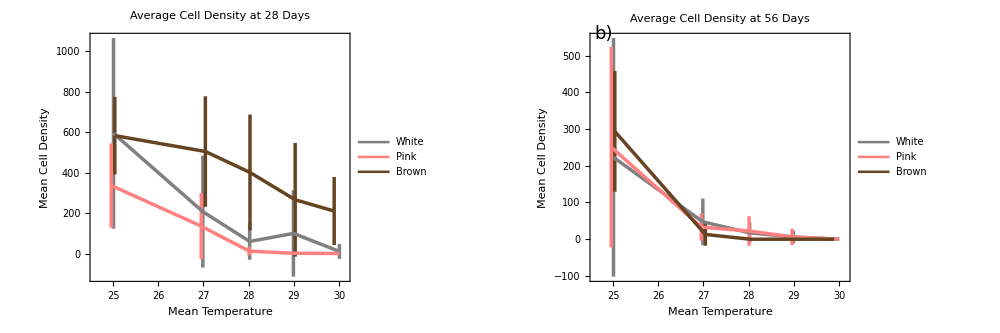

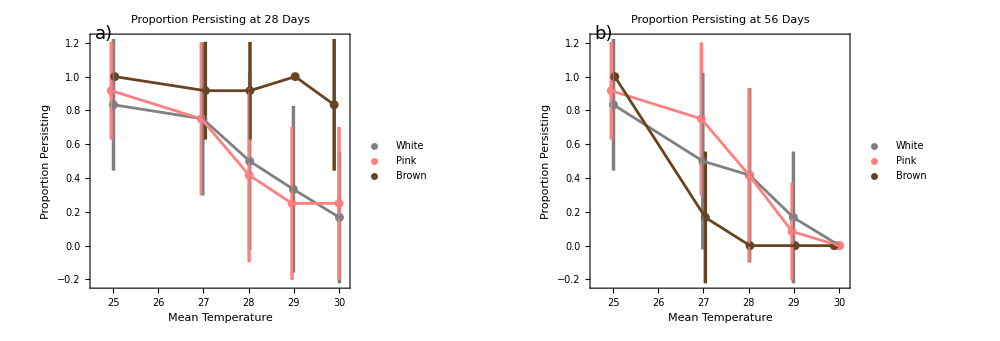

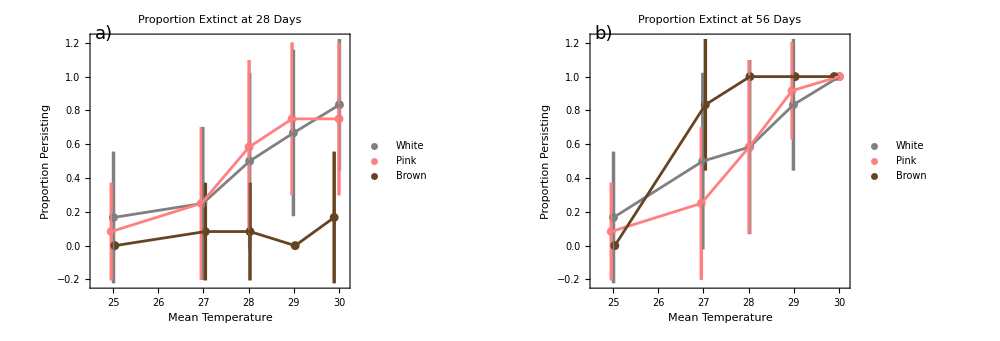

```mathematica
results=Import[directory<>"experimentalresults.csv","CSV"];

(*label all data*)
wmeantemps=results[[All,1]];
wsdtemps=results[[All,2]];
w28persist=results[[All,3]];
w56persist=results[[All,4]];
w28ext=results[[All,5]];
w56ext=results[[All,6]];
w28mpop=results[[All,7]];
w56mpop=results[[All,8]];
w28sdpop=results[[All,9]];
w56sdpop=results[[All,10]];

pmeantemps=results[[All,11]];
psdtemps=results[[All,12]];
p28persist=results[[All,13]];
p56persist=results[[All,14]];
p28ext=results[[All,15]];
p56ext=results[[All,16]];
p28mpop=results[[All,17]];
p56mpop=results[[All,18]];
p28sdpop=results[[All,19]];
p56sdpop=results[[All,20]];

bmeantemps=results[[All,21]];
bsdtemps=results[[All,22]];
b28persist=results[[All,23]];
b56persist=results[[All,24]];
b28ext=results[[All,25]];
b56ext=results[[All,26]];
b28mpop=results[[All,27]];
b56mpop=results[[All,28]];
b28sdpop=results[[All,29]];
b56sdpop=results[[All,30]];

w28extsd=results[[All,31]];
p28extsd=results[[All,32]];
b28extsd=results[[All,33]];
w56extsd=results[[All,34]];
p56extsd=results[[All,35]];
b56extsd=results[[All,36]];

(*pop density plots*)
w28density=Transpose[{wmeantemps,Around@@@Transpose[{w28mpop,w28sdpop}]}];
p28density=Transpose[{pmeantemps,Around@@@Transpose[{p28mpop,p28sdpop}]}];
b28density=Transpose[{bmeantemps,Around@@@Transpose[{b28mpop,b28sdpop}]}];
w56density=Transpose[{wmeantemps,Around@@@Transpose[{w56mpop,w56sdpop}]}];
p56density=Transpose[{pmeantemps,Around@@@Transpose[{p56mpop,p56sdpop}]}];
b56density=Transpose[{bmeantemps,Around@@@Transpose[{b56mpop,b56sdpop}]}];

thickness=.005;

density28=ListLinePlot[{w28density,p28density,b28density},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Average Cell Density at 28 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Right,Top}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Mean Cell Density"},LabelStyle->Directive[Black],ImageSize->500,
Epilog->{Text[Style["a)",Black,18],{24.8,1100}]}];
density56=ListLinePlot[{w56density,p56density,b56density},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Average Cell Density at 56 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Right,Top}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Mean Cell Density"},LabelStyle->Directive[Black],ImageSize->500,
Epilog->{Text[Style["b)",Black,18],{24.8,560}]}];
densities=GraphicsRow[{density28,density56},Spacings->0,ImageSize->1000]

(*persistence plots*)
w28p=Transpose[{wmeantemps,Around@@@Transpose[{w28persist,w28extsd}]}];
p28p=Transpose[{pmeantemps,Around@@@Transpose[{p28persist,p28extsd}]}];
b28p=Transpose[{bmeantemps,Around@@@Transpose[{b28persist,b28extsd}]}];
w56p=Transpose[{wmeantemps,Around@@@Transpose[{w56persist,w56extsd}]}];
p56p=Transpose[{pmeantemps,Around@@@Transpose[{p56persist,p56extsd}]}];
b56p=Transpose[{bmeantemps,Around@@@Transpose[{b56persist,b56extsd}]}];

persist28=Show[ListPlot[{w28p,p28p,b28p},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Proportion Persisting at 28 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Scaled[{0,0.32}],{0,0.5}}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Proportion Persisting"},LabelStyle->Directive[Black],ImageSize->500,
Epilog->{Text[Style["a)",Black,18],{24.8,1.25}]}],ListLinePlot[{w28p,p28p,b28p},PlotStyle->{Gray,Pink,Darker[Brown]}]];
persist56=Show[ListPlot[{w56p,p56p,b56p},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Proportion Persisting at 56 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Right,Top}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Proportion Persisting"},LabelStyle->Directive[Black],ImageSize->500,Epilog->{Text[Style["b)",Black,18],{24.8,1.25}]}],ListLinePlot[{w56p,p56p,b56p},PlotStyle->{Gray,Pink,Darker[Brown]}]];
persistence=GraphicsRow[{persist28,persist56},Spacings->0,ImageSize->1000]

(*extinction plots*)
w28e=Transpose[{wmeantemps,Around@@@Transpose[{w28ext,w28extsd}]}];
p28e=Transpose[{pmeantemps,Around@@@Transpose[{p28ext,p28extsd}]}];
b28e=Transpose[{bmeantemps,Around@@@Transpose[{b28ext,b28extsd}]}];
w56e=Transpose[{wmeantemps,Around@@@Transpose[{w56ext,w56extsd}]}];
p56e=Transpose[{pmeantemps,Around@@@Transpose[{p56ext,p56extsd}]}];
b56e=Transpose[{bmeantemps,Around@@@Transpose[{b56ext,b56extsd}]}];

extinct28=Show[ListPlot[{w28e,p28e,b28e},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Proportion Extinct at 28 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Scaled[{0,0.77}],{0,0.5}}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Proportion Persisting"},LabelStyle->Directive[Black],ImageSize->500,Epilog->{Text[Style["a)",Black,18],{24.8,1.25}]}],ListLinePlot[{w28e,p28e,b28e},PlotStyle->{Gray,Pink,Darker[Brown]}]];
extinct56=Show[ListPlot[{w56e,p56e,b56e},PlotRange->{{24.6,30.13},Automatic},PlotLabel->Style["Proportion Extinct at 56 Days",16],PlotStyle->{{Thickness[thickness],Gray},{Thickness[thickness],Pink},{Thickness[thickness],Darker[Brown]}},PlotLegends->Placed[{"White","Pink","Brown"},{Scaled[{0,0.77}],{0,0.5}}],Frame->{True,True,False,False},FrameStyle->16,FrameLabel->{"Mean Temperature","Proportion Persisting"},LabelStyle->Directive[Black],ImageSize->500,Epilog->{Text[Style["b)",Black,18],{24.8,1.25}]}],ListLinePlot[{w56e,p56e,b56e},PlotStyle->{Gray,Pink,Darker[Brown]}]];
extinct=GraphicsRow[{extinct28,extinct56},Spacings->0,ImageSize->1000]

Export[directory<>"densities.pdf",densities,"PDF",ImageResolution->1000];
Export[directory<>"persist.pdf",persistence,"PDF",ImageResolution->1000];
Export[directory<>"extinct.pdf",extinct,"PDF",ImageResolution->1000];
```